### Calculate G numerically

#### H(t)

```mathematica
Ht[Nl_, centre_, A_, ω_, t_, ϕ_]:= Table[If[Abs[i-j]==1, -1, If[i==j &&i == centre, A*Cos[ω*t + ϕ], 0]], {i, 1, Nl}, {j, 1, Nl}]
Ht[7, 4, A, ω, t, ϕ] // MatrixForm
```

(0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | -1 | A Cos[ϕ+t ω] | -1 | 0 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0)

#### Linear full chain

```mathematica
HLin[Nl_, centre_, A_, ω_, t_, ϕ_]:= Table[If[Abs[i-j]==1, -1, If[i==j, i*A*Cos[ω*t + ϕ], 0]], {i, 1, Nl}, {j, 1, Nl}]
HLin[7, 4, A, ω, t, ϕ] // MatrixForm
```

(A Cos[ϕ+t ω] | -1 | 0 | 0 | 0 | 0 | 0
-1 | 2 A Cos[ϕ+t ω] | -1 | 0 | 0 | 0 | 0
0 | -1 | 3 A Cos[ϕ+t ω] | -1 | 0 | 0 | 0
0 | 0 | -1 | 4 A Cos[ϕ+t ω] | -1 | 0 | 0
0 | 0 | 0 | -1 | 5 A Cos[ϕ+t ω] | -1 | 0
0 | 0 | 0 | 0 | -1 | 6 A Cos[ϕ+t ω] | -1
0 | 0 | 0 | 0 | 0 | -1 | 7 A Cos[ϕ+t ω])

#### Density Evolution, create U(T)

```mathematica
(*Notes on indexing;
A python matrix of 51x51 is indexed 0 ->50
A mathematica matrix of size 51x51 is indexed 1->51
pythonMatrix[25] is the 26th row of the matrix. There are 25 rows on either side. 
mathematicaMatrix[26] is the 26th row of the matrix. There are 25 rows on either side. *)
```

```mathematica
nLat = 51; (*size of lattice*)
aA = 30;   (*time dependent potential parameters*)
centre = 26; (*site of oscillation*)
phis = {0, Pi/7, Pi/6, Pi/5, Pi/4, Pi/3, Pi/2};

(*dataTable = {{"form", "a", "omega", "phi", "N", "hopping", "onsite", "next onsite", "NNN", "NNN overtop"}};*)
dataTable = Import["/Users/Georgia/Code/MBQD/floquet-simulations/data/analysis-G-mat.csv","Data"];
```

```mathematica
For[iP = 1, iP≤ 7, iP++,
ϕϕ = phis[[iP]];
Print[ϕϕ];

For[ ωω = 3.7, ωω ≤ 20, ωω += 1,
Print[ωω];
UT = Table[0, {i, 1, nLat},{j,1,nLat}];
T = 2π/ωω;
tf = T;

For[atomSiteStart=1,atomSiteStart≤nLat,atomSiteStart++,
ClearAll@ψ;
ψ0 = Table[If[i==atomSiteStart,1,0],{i,1,nLat}];
s=NDSolve[{-I *D[ψ[t], t]== HLin[nLat, centre, aA, ωω, t, ϕϕ].ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s]; 
ψT = Table[ψ[T][[1, i]], {i, 1, nLat}];
UT[[All, atomSiteStart]]= ψT
];
{eValsU, eVecs} = Eigensystem[UT];
eValsH = I*Log[eValsU] / T;
G = Chop[Sum[eValsH[[i]]*Outer[Times, eVecs[[i]], Conjugate[eVecs[[i]]]], {i, 1, nLat}]];
hopping = G[[centre,centre+1]];
onsite= G[[centre,centre]];
nextOnsite= G[[centre+1,centre+1]];
nnn= G[[centre,centre+2]];
nnnOvertop= G[[centre-1,centre+1]];
dataTable = Append[dataTable, {"Linear-m",Null, aA, ωω, N[ϕϕ], nLat, hopping, onsite, nextOnsite, nnn, nnnOvertop}];
];
Export["/Users/Georgia/Code/MBQD/floquet-simulations/data/analysis-G-mat.csv",dataTable];
];
Export["/Users/Georgia/Code/MBQD/floquet-simulations/data/analysis-G-mat.csv",dataTable];
```

0

3.7

4.7

5.7

6.7

7.7

8.7

9.7

10.7

11.7

12.7

13.7

14.7

15.7

16.7

17.7

18.7

19.7

π/7

3.7

4.7

5.7

6.7

7.7

8.7

9.7

10.7

11.7

12.7

13.7

14.7

15.7

16.7

17.7

18.7

19.7

π/6

3.7

4.7

```mathematica
Export["/Users/Georgia/Code/MBQD/floquet-simulations/data/analysis-G-mat.csv",
{{"form","rtol","a","omega","phi","N","hopping","onsite","next onsite","NNN","NNN overtop"}}];
```

#### Plot G for certain conditions

```mathematica
(*Calculate G*)
```

```mathematica
nLat = 51; (*size of lattice*)
UT = Table[0, {i, 1, nLat},{j,1,nLat}];
centre = 26; aA = 35;  
ϕϕ = π/7; ωω = 9.6;
T = 2π/ωω;
tf = T;

For[atomSiteStart=1,atomSiteStart≤nLat,atomSiteStart++,
ClearAll@ψ;
ψ0 = Table[If[i==atomSiteStart,1,0],{i,1,nLat}];
s=NDSolve[{-I *D[ψ[t], t]== Ht[nLat, centre, aA, ωω, t, ϕϕ].ψ[t], ψ[0] == ψ0}, ψ, {t, 0, tf}];
ψ[t_]=Evaluate[ψ[t]/.s]; 
ψT = Table[ψ[T][[1, i]], {i, 1, nLat}];
UT[[All, atomSiteStart]]= ψT
];
{eValsU, eVecs} = Eigensystem[UT];
eValsH = I*Log[eValsU] / T;
G = Chop[Sum[eValsH[[i]]*Outer[Times, eVecs[[i]], Conjugate[eVecs[[i]]]], {i, 1, nLat}]];
```

A = 35, ω = 9.6, ϕ = π/7

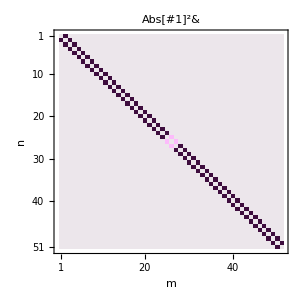
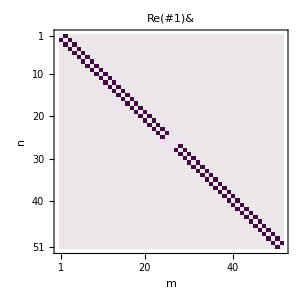
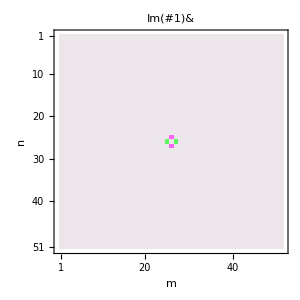

```mathematica
Print["A = ", aA, ", ω = ", ωω, ", ϕ = ", ϕϕ];Append[Table[MatrixPlot[f[G], FrameLabel->{"n","m"},   ImageSize-> {300,300}, ColorFunction->ColorData[{"GreenPinkTones", {-1, 1}}], ColorFunctionScaling->False, PlotLabel -> f], {f,{Abs[#]^2&,Re[#]&, Im[#]&}}], BarLegend[{"GreenPinkTones", {-1, 1}}]]
```

```mathematica
Export["/Users/Georgia/Code/MBQD/floquet-simulations/data/A35-w9p6-phpio7-G-mathematica-data.csv",G];
Export["/Users/Georgia/Code/MBQD/floquet-simulations/data/A35-w9p6-phpio7-G-mathematica-info.csv", 
{{"A", "omega", "phi/pi", "N", "centre"},
{aA, ωω, ϕϕ/π, nLat, centre }}];
```